# QHD-∞ Heisenberg Equations of Motion and the Cross Terms Approximation

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx

## Introduction

The evolution of the average of an observable A in the Heisenberg representation is given by the equation of motion (EOM): 
 ⅈ ℏ d/dt⟨A⟩=⟨[A,H]⟩
Consider the averages of momentum, position and their products ⟨p⟩, ⟨q⟩, ⟨p^2⟩, ⟨q^2⟩, ⟨pq⟩, ⟨p^3⟩, ⟨p^2 q⟩... The EOMs for the average values are coupled and, in general, form an infinite hierarchy of equations. This document shows how to get some of the equations of that infinite hierarchy. Subscripts will be used in this document to represent different particles (different modes). Products are symmetrized, for example ⟨p_1·q_1⟩_s=⟨(p_1·q_1+q_1·p_1)/2⟩, and cross terms are approximated, for instance ⟨p_1·p_2⟩≈⟨p_1⟩⟨p_2⟩. Here we obtain equations from the appendix of Pahl and Prezhdo in J. Chem Phys. Vol 116 No. 20, May 2002, Pages 8704-8712
 http://homepage.cem.itesm.mx/lgomez/quantum/QHDHigherOrders.pdf .
Calculations are performed using QUANTUM, a free Mathematica add-on that can be downloaded from:
 http://homepage.cem.itesm.mx/lgomez/quantum/

## Load the Package

First load the Quantum`QHD` package. Write:
Needs["Quantum`QHD`"]
then press at the same time the keys ⇧-⌤ to evaluate. Mathematica will load the package and print a welcome message:

```mathematica
Needs["Quantum`QHD`"]
```

Quantum`QHD` 
A Mathematica package for Quantized Hamilton Dynamics approximation to Heisenberg Equations of Motion
by José Luis Gómez-Muñoz
based on the original idea of Kirill Igumenshchev

This add-on does NOT work properly with the debugger turned on. Therefore the debugger must NOT be checked in the Evaluation menu of Mathematica.

Execute SetQHDAliases[] in order to use the keyboard to enter QHD objects
SetQHDAliases[] must be executed again in each new notebook that is created

In order to use the keyboard to enter quantum objects write:
SetQHDAliases[ ];
then press at the same time the keys ⇧-⌤ to evaluate. Remember that SetQuantumAliases[ ] must be evaluated again in each new notebook:

```mathematica
SetQHDAliases[]
```

ALIASES:
[ESC]on[ESC]     · Quantum concatenation symbol
[ESC]time[ESC]   𝓉 Time symbol
[ESC]hb[ESC]     ℏ Reduced Planck's constant (h bar)
[ESC]ii[ESC]     ⅈ Imaginary I symbol
[ESC]inf[ESC]    ∞ Infinity symbol
[ESC]->[ESC]     → Option (Rule) symbol
[ESC]ave[ESC]    ⟨□⟩ Quantum average template
[ESC]expec[ESC]  ⟨□⟩ Quantum average template
[ESC]symm[ESC]   (□·□)_𝓈 Symmetrized quantum product template
[ESC]comm[ESC]   ⟦□,□⟧_- Commutator template
[ESC]po[ESC]     (□)^□ Power template
[ESC]su[ESC]     □_□ Subscripted variable template
[ESC]posu[ESC]   □_□^□ Power of a subscripted variable template
[ESC]fra[ESC]    □/□ Fraction template
[ESC]eva[ESC]    □/.{□→□,□→□} Evaluation (ReplaceAll) template

SetQHDAliases[] must be executed again in each new notebook that is created, only one time per notebook.

## Commutation Relationships and Hamiltonian J. Chem. Phys. Vol 116 No. 20, May 2002, Pages 8704-8712

This Hamiltoninan and commutation relationships are those used by E. Pahl and O V. Prezhdo in their paper.
In order to enter the templates and symbols □_□, □_□^□, ⟦□,□⟧_- and ⅈ you can either use the QHD palette (toolbar) or press the keys [ESC]su[ESC], [ESC]supo[ESC], [ESC]comm[ESC] and [ESC]ii[ESC]. The Hamiltonian that will be used in this document is stored in the variable ifnh below:

```mathematica
SetQuantumObject[q,p];
⟦Subscript[q, 1],Subscript[p, 1]⟧_-=ⅈ*ℏ;
⟦Subscript[q, 2],Subscript[p, 2]⟧_-=ⅈ*ℏ;
⟦Subscript[q, 1],Subscript[p, 2]⟧_-=0;
⟦Subscript[q, 2],Subscript[p, 1]⟧_-=0;
⟦Subscript[q, 1],Subscript[q, 2]⟧_-=0;
⟦Subscript[p, 1],Subscript[p, 2]⟧_-=0;
infh=Subscript[k, 1]/2 Subscript[p, 1]^2+Subscript[a, 2]/2 Subscript[q, 1]^2+Subscript[k, 2]/2 Subscript[p, 2]^2+Subscript[b, 1]*Subscript[q, 2]+1/2 Subscript[b, 2]*Subscript[q, 2]^2+Subscript[b, 3]/3 Subscript[q, 2]^3+λ*Subscript[q, 1]^2·Subscript[q, 2]
```

1/2 k_1 p_1^2+1/2 k_2 p_2^2+1/2 a_2 q_1^2+b_1 q_2+1/2 b_2 q_2^2+1/3 b_3 q_2^3+λ q_1^2·q_2

## Heisenberg Equations of Motion (EOM)

The Heisenberg EOM: 
ⅈ ℏ d/dt⟨p_1⟩=⟨[p_1,H]⟩
can be calculated using the QHD-Mathematica command QHDEOM, as shown below. The first argument specifies the QHD-order, which is set below to ∞ (type [ESC]inf[ESC]) so that no QHD closure is done. The second argument is the observable, p_1 in this example. The third argument is the Hamiltonian, remember that it was stored in variable infh above in this document. The output of QHDEOM can be stored in a variable; it is stored in infeom, then it is shown in a nice format with the command QHDForm below:

```mathematica
infeom=QHDEOM[∞,Subscript[p, 1],infh];
QHDForm[infeom]
```

No closure was applied
QHDApproximantFunction->QHDCrossTermsApproximant. 
(d⟨p_1⟩)/d𝓉=-a_2 ⟨q_1⟩-2 λ ⟨q_1⟩ ⟨q_2⟩

The command QHDDifferentialEquations formats the output of QHDEOM as a standard Mathematica equation, as those that can be part of the input of standard Mathematica commands like DSolve and NDSolve. The output infeom that was stored above is formated that way below:

```mathematica
QHDDifferentialEquations[infeom]
```

{⟨p_1⟩'[𝓉]==-a_2 ⟨q_1⟩[𝓉]-2 λ ⟨q_1⟩[𝓉] ⟨q_2⟩[𝓉]}

A different symbol for time can be specified. The operator → can be entered pressing the keys [ESC][MINUS][GREATERTHAN][ESC], see the equations below:

```mathematica
QHDDifferentialEquations[infeom,QHDSymbolForTime->var]
```

{⟨p_1⟩'[var]==-a_2 ⟨q_1⟩[var]-2 λ ⟨q_1⟩[var] ⟨q_2⟩[var]}

## Hierarchy of Heisenberg EOMs

The EOM calculated above for ⟨p_1⟩ depends on ⟨q_1⟩ and ⟨q_2⟩. The EOM of those two average values will depend on other new ones, like ⟨p_2⟩ and ⟨p_1·q_1⟩, and so on, thus an infinite hierarchy of equations is obtained. The command QHDHierarchy can be used in oder to obtain the first few equations of that hierarchy. It has the same syntax as the command QHDEOM that was used above; the first argument specifies the QHD-order, which is set below to ∞ so that no QHD closure is done. The second argument is the initial observable, p_1 in this example. The third argument is the Hamiltonian, remember that it was stored in variable infh above in this document. This hierarchy of equations is infinite, calculations stop at second order in the products of the observables. Those products are symmetrized, for example ⟨p_1·q_1⟩_s=⟨(p_1·q_1+q_1·p_1)/2⟩, and cross terms are approximated, for instance ⟨p_1·p_2⟩≈⟨p_1⟩⟨p_2⟩.  The output of QHDHierarchy is stored in the variable infhier, and it is shown using the QHDForm command below:

```mathematica
infhier=QHDHierarchy[∞,Subscript[p, 1],infh];
QHDForm[ infhier ]
```

Calculations were stopped at order QHDMaxOrder→2
QHDApproximantFunction->QHDCrossTermsApproximant. 
(d⟨p_1⟩)/d𝓉=-a_2 ⟨q_1⟩-2 λ ⟨q_1⟩ ⟨q_2⟩
(d⟨q_1⟩)/d𝓉=k_1 ⟨p_1⟩
(d⟨q_2⟩)/d𝓉=k_2 ⟨p_2⟩
(d⟨p_2⟩)/d𝓉=-b_1-λ ⟨q_1^2⟩-b_2 ⟨q_2⟩-b_3 ⟨q_2^2⟩
(d⟨q_1^2⟩)/d𝓉=2 k_1 ⟨p_1 q_1⟩_𝓈
(d⟨q_2^2⟩)/d𝓉=2 k_2 ⟨p_2 q_2⟩_𝓈
(d⟨p_1 q_1⟩_𝓈)/d𝓉=k_1 ⟨p_1^2⟩-a_2 ⟨q_1^2⟩-2 λ ⟨q_1^2⟩ ⟨q_2⟩
(d⟨p_2 q_2⟩_𝓈)/d𝓉=k_2 ⟨p_2^2⟩-b_1 ⟨q_2⟩-λ ⟨q_1^2⟩ ⟨q_2⟩-b_2 ⟨q_2^2⟩-b_3 ⟨q_2^3⟩
(d⟨p_1^2⟩)/d𝓉=-2 a_2 ⟨p_1 q_1⟩_𝓈-4 λ ⟨q_2⟩ ⟨p_1 q_1⟩_𝓈
(d⟨p_2^2⟩)/d𝓉=-2 b_1 ⟨p_2⟩-2 λ ⟨p_2⟩ ⟨q_1^2⟩-2 b_2 ⟨p_2 q_2⟩_𝓈-2 b_3 ⟨p_2 q_2^2⟩_𝓈

Not all the variables have their EOM included in the hierarchy, because infinite order ∞ means that no closure procedure was applied. The command QHDForm accepts the option QHDNeedClosureStyle, which allows to specify a different style for those variables whose EOM is not included in the hierarchy, see the bottom of the table below:

```mathematica
QHDForm[ infhier, QHDNeedClosureStyle->{Bold,Larger,Blue} ]
```

Calculations were stopped at order QHDMaxOrder→2
QHDApproximantFunction->QHDCrossTermsApproximant. 
(d⟨p_1⟩)/d𝓉=-a_2 ⟨q_1⟩-2 λ ⟨q_1⟩ ⟨q_2⟩
(d⟨q_1⟩)/d𝓉=k_1 ⟨p_1⟩
(d⟨q_2⟩)/d𝓉=k_2 ⟨p_2⟩
(d⟨p_2⟩)/d𝓉=-b_1-λ ⟨q_1^2⟩-b_2 ⟨q_2⟩-b_3 ⟨q_2^2⟩
(d⟨q_1^2⟩)/d𝓉=2 k_1 ⟨p_1 q_1⟩_𝓈
(d⟨q_2^2⟩)/d𝓉=2 k_2 ⟨p_2 q_2⟩_𝓈
(d⟨p_1 q_1⟩_𝓈)/d𝓉=k_1 ⟨p_1^2⟩-a_2 ⟨q_1^2⟩-2 λ ⟨q_1^2⟩ ⟨q_2⟩
(d⟨p_2 q_2⟩_𝓈)/d𝓉=-⟨q_2^3⟩ b_3+k_2 ⟨p_2^2⟩-b_1 ⟨q_2⟩-λ ⟨q_1^2⟩ ⟨q_2⟩-b_2 ⟨q_2^2⟩
(d⟨p_1^2⟩)/d𝓉=-2 a_2 ⟨p_1 q_1⟩_𝓈-4 λ ⟨q_2⟩ ⟨p_1 q_1⟩_𝓈
(d⟨p_2^2⟩)/d𝓉=-2 ⟨p_2 q_2^2⟩_𝓈 b_3-2 b_1 ⟨p_2⟩-2 λ ⟨p_2⟩ ⟨q_1^2⟩-2 b_2 ⟨p_2 q_2⟩_𝓈

A hierarchy can be shown in a graph using the command QHDGraphPlot on the output of QHDHierachy. Each arrow points from a first dynamical variable to a second dynamical variable that includes the first one in its EOM; please compare the table above with the graph below:

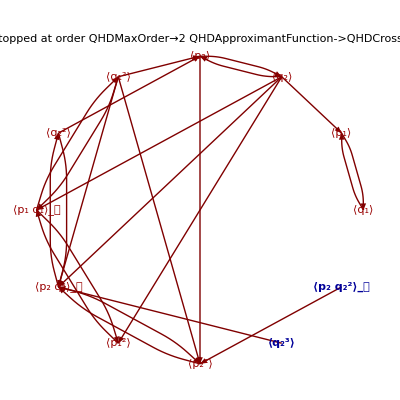

```mathematica
QHDGraphPlot[infhier]
```

The command QHDDifferentialEquations formats the output of QHDHierarchy as standard Mathematica equations, as those that can be part of the input of standard Mathematica commands like DSolve and NDSolve. The output infhier that was stored above is formated that way below:

```mathematica
QHDDifferentialEquations[infhier]
```

{⟨p_1⟩'[𝓉]==-a_2 ⟨q_1⟩[𝓉]-2 λ ⟨q_1⟩[𝓉] ⟨q_2⟩[𝓉],⟨q_1⟩'[𝓉]==k_1 ⟨p_1⟩[𝓉],⟨q_2⟩'[𝓉]==k_2 ⟨p_2⟩[𝓉],⟨p_2⟩'[𝓉]==-b_1-λ ⟨q_1^2⟩[𝓉]-b_2 ⟨q_2⟩[𝓉]-b_3 ⟨q_2^2⟩[𝓉],⟨q_1^2⟩'[𝓉]==2 k_1 ⟨(p_1·q_1)_𝓈⟩[𝓉],⟨q_2^2⟩'[𝓉]==2 k_2 ⟨(p_2·q_2)_𝓈⟩[𝓉],⟨(p_1·q_1)_𝓈⟩'[𝓉]==k_1 ⟨p_1^2⟩[𝓉]-a_2 ⟨q_1^2⟩[𝓉]-2 λ ⟨q_1^2⟩[𝓉] ⟨q_2⟩[𝓉],⟨(p_2·q_2)_𝓈⟩'[𝓉]==k_2 ⟨p_2^2⟩[𝓉]-b_1 ⟨q_2⟩[𝓉]-λ ⟨q_1^2⟩[𝓉] ⟨q_2⟩[𝓉]-b_2 ⟨q_2^2⟩[𝓉]-b_3 ⟨q_2^3⟩[𝓉],⟨p_1^2⟩'[𝓉]==-2 a_2 ⟨(p_1·q_1)_𝓈⟩[𝓉]-4 λ ⟨q_2⟩[𝓉] ⟨(p_1·q_1)_𝓈⟩[𝓉],⟨p_2^2⟩'[𝓉]==-2 b_1 ⟨p_2⟩[𝓉]-2 λ ⟨p_2⟩[𝓉] ⟨q_1^2⟩[𝓉]-2 b_2 ⟨(p_2·q_2)_𝓈⟩[𝓉]-2 b_3 ⟨(p_2·q_2^2)_𝓈⟩[𝓉]}

A different symbol for time can be specified. The operator → can be entered pressing the keys [ESC][MINUS][GREATERTHAN][ESC], see the equations below:

```mathematica
QHDDifferentialEquations[infhier,QHDSymbolForTime->z]
```

{⟨p_1⟩'[z]==-a_2 ⟨q_1⟩[z]-2 λ ⟨q_1⟩[z] ⟨q_2⟩[z],⟨q_1⟩'[z]==k_1 ⟨p_1⟩[z],⟨q_2⟩'[z]==k_2 ⟨p_2⟩[z],⟨p_2⟩'[z]==-b_1-λ ⟨q_1^2⟩[z]-b_2 ⟨q_2⟩[z]-b_3 ⟨q_2^2⟩[z],⟨q_1^2⟩'[z]==2 k_1 ⟨(p_1·q_1)_𝓈⟩[z],⟨q_2^2⟩'[z]==2 k_2 ⟨(p_2·q_2)_𝓈⟩[z],⟨(p_1·q_1)_𝓈⟩'[z]==k_1 ⟨p_1^2⟩[z]-a_2 ⟨q_1^2⟩[z]-2 λ ⟨q_1^2⟩[z] ⟨q_2⟩[z],⟨(p_2·q_2)_𝓈⟩'[z]==k_2 ⟨p_2^2⟩[z]-b_1 ⟨q_2⟩[z]-λ ⟨q_1^2⟩[z] ⟨q_2⟩[z]-b_2 ⟨q_2^2⟩[z]-b_3 ⟨q_2^3⟩[z],⟨p_1^2⟩'[z]==-2 a_2 ⟨(p_1·q_1)_𝓈⟩[z]-4 λ ⟨q_2⟩[z] ⟨(p_1·q_1)_𝓈⟩[z],⟨p_2^2⟩'[z]==-2 b_1 ⟨p_2⟩[z]-2 λ ⟨p_2⟩[z] ⟨q_1^2⟩[z]-2 b_2 ⟨(p_2·q_2)_𝓈⟩[z]-2 b_3 ⟨(p_2·q_2^2)_𝓈⟩[z]}

## Cross Terms Approximations

The command QHDHierarchy accepts several options, among then QHDApproximantFunction, see the evaluation below:

```mathematica
Options[QHDHierarchy]
```

{QHDMaxOrder→2,QHDHBar→ℏ,QHDLabel→Automatic,QHDApproximantFunction→QHDCrossTermsApproximant}

The default approximant is QHDCrossTermsApproximant, we can see what is the effect of this approximant below:

```mathematica
?QHDCrossTermsApproximant
```

QHDCrossTermsApproximant[expr] approximates expected values of crossterms ⟨p_1^n·p_2^m⟩≈⟨p_1^n⟩⟨p_2^m⟩ in expr

## EOM Hierarchy without Cross Terms Approximation

We can get another hierarchy for the same problem without the cross terms approximation, adding as a last argument of QHDHierarchy the option QHDApproximantFunction→Identity, as shown below:

```mathematica
infhierNoApp=QHDHierarchy[∞,Subscript[p, 1],infh,QHDApproximantFunction->Identity];
QHDForm[ infhierNoApp ]
```

Calculations were stopped at order QHDMaxOrder→2
(d⟨p_1⟩)/d𝓉=-a_2 ⟨q_1⟩-2 λ ⟨q_1 q_2⟩_𝓈
(d⟨q_1⟩)/d𝓉=k_1 ⟨p_1⟩
(d⟨q_1 q_2⟩_𝓈)/d𝓉=k_2 ⟨p_2 q_1⟩_𝓈+k_1 ⟨p_1 q_2⟩_𝓈
(d⟨p_2 q_1⟩_𝓈)/d𝓉=-b_1 ⟨q_1⟩-λ ⟨q_1^3⟩+k_1 ⟨p_1 p_2⟩_𝓈-b_2 ⟨q_1 q_2⟩_𝓈-b_3 ⟨q_1 q_2^2⟩_𝓈
(d⟨p_1 q_2⟩_𝓈)/d𝓉=k_2 ⟨p_1 p_2⟩_𝓈-a_2 ⟨q_1 q_2⟩_𝓈-2 λ ⟨q_1 q_2^2⟩_𝓈
(d⟨p_1 p_2⟩_𝓈)/d𝓉=-b_1 ⟨p_1⟩-a_2 ⟨p_2 q_1⟩_𝓈-λ ⟨p_1 q_1^2⟩_𝓈-b_2 ⟨p_1 q_2⟩_𝓈-b_3 ⟨p_1 q_2^2⟩_𝓈-2 λ ⟨p_2 q_1 q_2⟩_𝓈

A hierarchy can be shown in a graph using the command QHDGraphPlot on the output of QHDHierachy. Each arrow points from a first dynamical variable to a second dynamical variable that includes the first one in its EOM; please compare the table above with the graph below:

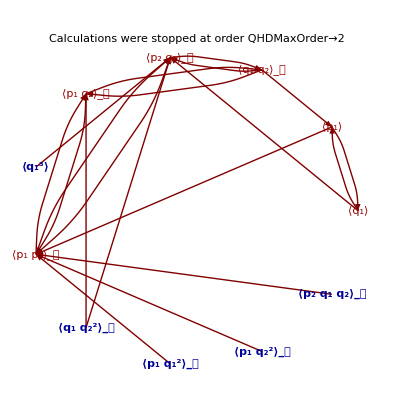

```mathematica
QHDGraphPlot[ infhierNoApp ]
```

Products of operators were symmetrized, for example: ⟨p_2·q_1·q_2⟩_𝓈=1/2⟨p_2·q_1·q_2⟩+1/2⟨q_2·q_1·p_2⟩

## Hierarchy Up To Third Order

QHDHierarchy stops calculating EOM up to the order specified by its option QHDMaxOrder, which has a default value of 2. Here we obtain the hierarchy up to order 3, this calculation takes several minutes in a laptop computer, see the table below:

```mathematica
infhier3=QHDHierarchy[∞,Subscript[p, 1],infh,QHDMaxOrder->3];
QHDForm[ infhier3 ]
```

Calculations were stopped at order QHDMaxOrder→3
QHDApproximantFunction->QHDCrossTermsApproximant. 
(d⟨p_1⟩)/d𝓉=-a_2 ⟨q_1⟩-2 λ ⟨q_1⟩ ⟨q_2⟩
(d⟨q_1⟩)/d𝓉=k_1 ⟨p_1⟩
(d⟨q_2⟩)/d𝓉=k_2 ⟨p_2⟩
(d⟨p_2⟩)/d𝓉=-b_1-λ ⟨q_1^2⟩-b_2 ⟨q_2⟩-b_3 ⟨q_2^2⟩
(d⟨q_1^2⟩)/d𝓉=2 k_1 ⟨p_1 q_1⟩_𝓈
(d⟨q_2^2⟩)/d𝓉=2 k_2 ⟨p_2 q_2⟩_𝓈
(d⟨p_1 q_1⟩_𝓈)/d𝓉=k_1 ⟨p_1^2⟩-a_2 ⟨q_1^2⟩-2 λ ⟨q_1^2⟩ ⟨q_2⟩
(d⟨p_2 q_2⟩_𝓈)/d𝓉=k_2 ⟨p_2^2⟩-b_1 ⟨q_2⟩-λ ⟨q_1^2⟩ ⟨q_2⟩-b_2 ⟨q_2^2⟩-b_3 ⟨q_2^3⟩
(d⟨p_1^2⟩)/d𝓉=-2 a_2 ⟨p_1 q_1⟩_𝓈-4 λ ⟨q_2⟩ ⟨p_1 q_1⟩_𝓈
(d⟨p_2^2⟩)/d𝓉=-2 b_1 ⟨p_2⟩-2 λ ⟨p_2⟩ ⟨q_1^2⟩-2 b_2 ⟨p_2 q_2⟩_𝓈-2 b_3 ⟨p_2 q_2^2⟩_𝓈
(d⟨q_2^3⟩)/d𝓉=3 k_2 ⟨p_2 q_2^2⟩_𝓈
(d⟨p_2 q_2^2⟩_𝓈)/d𝓉=-b_1 ⟨q_2^2⟩-λ ⟨q_1^2⟩ ⟨q_2^2⟩-b_2 ⟨q_2^3⟩-b_3 ⟨q_2^4⟩+2 k_2 ⟨p_2^2 q_2⟩_𝓈
(d⟨p_2^2 q_2⟩_𝓈)/d𝓉=k_2 ⟨p_2^3⟩-2 b_1 ⟨p_2 q_2⟩_𝓈-2 λ ⟨q_1^2⟩ ⟨p_2 q_2⟩_𝓈-2 b_2 ⟨p_2 q_2^2⟩_𝓈-2 b_3 ⟨p_2 q_2^3⟩_𝓈
(d⟨p_2^3⟩)/d𝓉=-ℏ^2 b_3-3 b_1 ⟨p_2^2⟩-3 λ ⟨p_2^2⟩ ⟨q_1^2⟩-3 b_2 ⟨p_2^2 q_2⟩_𝓈-3 b_3 ⟨p_2^2 q_2^2⟩_𝓈

A hierarchy can be shown in a graph using the command QHDGraphPlot on the output of QHDHierachy. Each arrow points from a first dynamical variable to a second dynamical variable that includes the first one in its EOM; please compare the table above with the graph below:

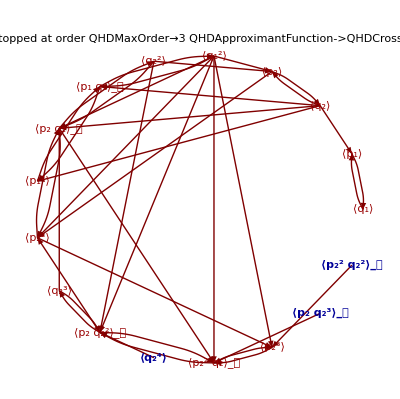

```mathematica
QHDGraphPlot[infhier3]
```

## EOM Hierarchy Up To Fourth Order

Here we obtain the hierarchy up to order 4, this calculation takes several minutes in a laptop computer, see the table below:

```mathematica
infhier4=QHDHierarchy[∞,Subscript[p, 1],infh,QHDMaxOrder->4];
QHDForm[ infhier4 ]
```

Calculations were stopped at order QHDMaxOrder→4
QHDApproximantFunction->QHDCrossTermsApproximant. 
(d⟨p_1⟩)/d𝓉=-a_2 ⟨q_1⟩-2 λ ⟨q_1⟩ ⟨q_2⟩
(d⟨q_1⟩)/d𝓉=k_1 ⟨p_1⟩
(d⟨q_2⟩)/d𝓉=k_2 ⟨p_2⟩
(d⟨p_2⟩)/d𝓉=-b_1-λ ⟨q_1^2⟩-b_2 ⟨q_2⟩-b_3 ⟨q_2^2⟩
(d⟨q_1^2⟩)/d𝓉=2 k_1 ⟨p_1 q_1⟩_𝓈
(d⟨q_2^2⟩)/d𝓉=2 k_2 ⟨p_2 q_2⟩_𝓈
(d⟨p_1 q_1⟩_𝓈)/d𝓉=k_1 ⟨p_1^2⟩-a_2 ⟨q_1^2⟩-2 λ ⟨q_1^2⟩ ⟨q_2⟩
(d⟨p_2 q_2⟩_𝓈)/d𝓉=k_2 ⟨p_2^2⟩-b_1 ⟨q_2⟩-λ ⟨q_1^2⟩ ⟨q_2⟩-b_2 ⟨q_2^2⟩-b_3 ⟨q_2^3⟩
(d⟨p_1^2⟩)/d𝓉=-2 a_2 ⟨p_1 q_1⟩_𝓈-4 λ ⟨q_2⟩ ⟨p_1 q_1⟩_𝓈
(d⟨p_2^2⟩)/d𝓉=-2 b_1 ⟨p_2⟩-2 λ ⟨p_2⟩ ⟨q_1^2⟩-2 b_2 ⟨p_2 q_2⟩_𝓈-2 b_3 ⟨p_2 q_2^2⟩_𝓈
(d⟨q_2^3⟩)/d𝓉=3 k_2 ⟨p_2 q_2^2⟩_𝓈
(d⟨p_2 q_2^2⟩_𝓈)/d𝓉=-b_1 ⟨q_2^2⟩-λ ⟨q_1^2⟩ ⟨q_2^2⟩-b_2 ⟨q_2^3⟩-b_3 ⟨q_2^4⟩+2 k_2 ⟨p_2^2 q_2⟩_𝓈
(d⟨q_2^4⟩)/d𝓉=4 k_2 ⟨p_2 q_2^3⟩_𝓈
(d⟨p_2^2 q_2⟩_𝓈)/d𝓉=k_2 ⟨p_2^3⟩-2 b_1 ⟨p_2 q_2⟩_𝓈-2 λ ⟨q_1^2⟩ ⟨p_2 q_2⟩_𝓈-2 b_2 ⟨p_2 q_2^2⟩_𝓈-2 b_3 ⟨p_2 q_2^3⟩_𝓈
(d⟨p_2 q_2^3⟩_𝓈)/d𝓉=(3 ℏ^2 k_2)/2-b_1 ⟨q_2^3⟩-λ ⟨q_1^2⟩ ⟨q_2^3⟩-b_2 ⟨q_2^4⟩-b_3 ⟨q_2^5⟩+3 k_2 ⟨p_2^2 q_2^2⟩_𝓈
(d⟨p_2^3⟩)/d𝓉=-ℏ^2 b_3-3 b_1 ⟨p_2^2⟩-3 λ ⟨p_2^2⟩ ⟨q_1^2⟩-3 b_2 ⟨p_2^2 q_2⟩_𝓈-3 b_3 ⟨p_2^2 q_2^2⟩_𝓈
(d⟨p_2^2 q_2^2⟩_𝓈)/d𝓉=2 k_2 ⟨p_2^3 q_2⟩_𝓈-2 b_1 ⟨p_2 q_2^2⟩_𝓈-2 λ ⟨q_1^2⟩ ⟨p_2 q_2^2⟩_𝓈-2 b_2 ⟨p_2 q_2^3⟩_𝓈-2 b_3 ⟨p_2 q_2^4⟩_𝓈
(d⟨p_2^3 q_2⟩_𝓈)/d𝓉=-3/2 ℏ^2 b_2+k_2 ⟨p_2^4⟩-4 ℏ^2 b_3 ⟨q_2⟩-3 b_1 ⟨p_2^2 q_2⟩_𝓈-3 λ ⟨q_1^2⟩ ⟨p_2^2 q_2⟩_𝓈-3 b_2 ⟨p_2^2 q_2^2⟩_𝓈-3 b_3 ⟨p_2^2 q_2^3⟩_𝓈
(d⟨p_2^4⟩)/d𝓉=-4 ℏ^2 b_3 ⟨p_2⟩-4 b_1 ⟨p_2^3⟩-4 λ ⟨p_2^3⟩ ⟨q_1^2⟩-4 b_2 ⟨p_2^3 q_2⟩_𝓈-4 b_3 ⟨p_2^3 q_2^2⟩_𝓈

A hierarchy can be shown in a graph using the command QHDGraphPlot on the output of QHDHierachy. Each arrow points from a first dynamical variable to a second dynamical variable that includes the first one in its EOM; please compare the table above with the graph below:

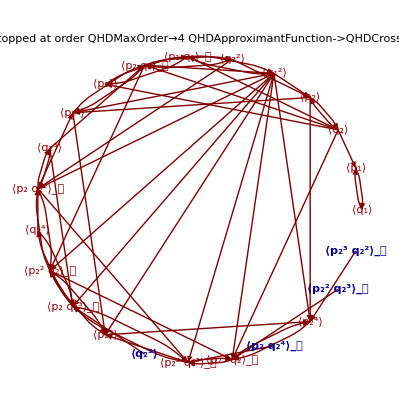

```mathematica
QHDGraphPlot[infhier4]
```

## Saving the QHD hierarchies for future use

The calculation QHD hierarchies is time consuming, therefore it is a good idea to save them for future use. The simplest way to do it is using the standard Mathematica command Put. The QHD hierarchy is stored in the file hier4.m, see the command below:

```mathematica
Put[infhier4,"hier4.m"]
```

The command FileNames[“*.m”] can be used to see the files that were created by the command Put (together with any other preexisting file with .m extension), see the command below:

```mathematica
FileNames["*.m"]
```

{hier4.m,qhd2.m,qhd3.m,qhd4.m}

## Loading and Formating the Hierarchy

Next commands have been written as they would be used in a different Mathematica session, using the command Get to load the hierarchy that was saved above (instead of calculating it again). Notice that the commutation relation and the Hamiltonian are defined again, and its important to use those that correspond to the hierarchy that is loaded. The hierarchy is shown below:

```mathematica
Needs["Quantum`QHD`"];
SetQHDAliases[];
SetQuantumObject[q,p];
⟦Subscript[q, 1],Subscript[p, 1]⟧_-=ⅈ*ℏ;
⟦Subscript[q, 2],Subscript[p, 2]⟧_-=ⅈ*ℏ;
⟦Subscript[q, 1],Subscript[p, 2]⟧_-=0;
⟦Subscript[q, 2],Subscript[p, 1]⟧_-=0;
⟦Subscript[q, 1],Subscript[q, 2]⟧_-=0;
⟦Subscript[p, 1],Subscript[p, 2]⟧_-=0;
infh=Subscript[k, 1]/2 Subscript[p, 1]^2+Subscript[a, 2]/2 Subscript[q, 1]^2+Subscript[k, 2]/2 Subscript[p, 2]^2+Subscript[b, 1]*Subscript[q, 2]+1/2 Subscript[b, 2]*Subscript[q, 2]^2+Subscript[b, 3]/3 Subscript[q, 2]^3+λ*Subscript[q, 1]^2·Subscript[q, 2];
myhierarchy=Get["hier4.m"];
QHDForm[ myhierarchy]
```

Calculations were stopped at order QHDMaxOrder→4
QHDApproximantFunction->QHDCrossTermsApproximant. 
(d⟨p_1⟩)/d𝓉=-a_2 ⟨q_1⟩-2 λ ⟨q_1⟩ ⟨q_2⟩
(d⟨q_1⟩)/d𝓉=k_1 ⟨p_1⟩
(d⟨q_2⟩)/d𝓉=k_2 ⟨p_2⟩
(d⟨p_2⟩)/d𝓉=-b_1-λ ⟨q_1^2⟩-b_2 ⟨q_2⟩-b_3 ⟨q_2^2⟩
(d⟨q_1^2⟩)/d𝓉=2 k_1 ⟨p_1 q_1⟩_𝓈
(d⟨q_2^2⟩)/d𝓉=2 k_2 ⟨p_2 q_2⟩_𝓈
(d⟨p_1 q_1⟩_𝓈)/d𝓉=k_1 ⟨p_1^2⟩-a_2 ⟨q_1^2⟩-2 λ ⟨q_1^2⟩ ⟨q_2⟩
(d⟨p_2 q_2⟩_𝓈)/d𝓉=k_2 ⟨p_2^2⟩-b_1 ⟨q_2⟩-λ ⟨q_1^2⟩ ⟨q_2⟩-b_2 ⟨q_2^2⟩-b_3 ⟨q_2^3⟩
(d⟨p_1^2⟩)/d𝓉=-2 a_2 ⟨p_1 q_1⟩_𝓈-4 λ ⟨q_2⟩ ⟨p_1 q_1⟩_𝓈
(d⟨p_2^2⟩)/d𝓉=-2 b_1 ⟨p_2⟩-2 λ ⟨p_2⟩ ⟨q_1^2⟩-2 b_2 ⟨p_2 q_2⟩_𝓈-2 b_3 ⟨p_2 q_2^2⟩_𝓈
(d⟨q_2^3⟩)/d𝓉=3 k_2 ⟨p_2 q_2^2⟩_𝓈
(d⟨p_2 q_2^2⟩_𝓈)/d𝓉=-b_1 ⟨q_2^2⟩-λ ⟨q_1^2⟩ ⟨q_2^2⟩-b_2 ⟨q_2^3⟩-b_3 ⟨q_2^4⟩+2 k_2 ⟨p_2^2 q_2⟩_𝓈
(d⟨q_2^4⟩)/d𝓉=4 k_2 ⟨p_2 q_2^3⟩_𝓈
(d⟨p_2^2 q_2⟩_𝓈)/d𝓉=k_2 ⟨p_2^3⟩-2 b_1 ⟨p_2 q_2⟩_𝓈-2 λ ⟨q_1^2⟩ ⟨p_2 q_2⟩_𝓈-2 b_2 ⟨p_2 q_2^2⟩_𝓈-2 b_3 ⟨p_2 q_2^3⟩_𝓈
(d⟨p_2 q_2^3⟩_𝓈)/d𝓉=(3 ℏ^2 k_2)/2-b_1 ⟨q_2^3⟩-λ ⟨q_1^2⟩ ⟨q_2^3⟩-b_2 ⟨q_2^4⟩-b_3 ⟨q_2^5⟩+3 k_2 ⟨p_2^2 q_2^2⟩_𝓈
(d⟨p_2^3⟩)/d𝓉=-ℏ^2 b_3-3 b_1 ⟨p_2^2⟩-3 λ ⟨p_2^2⟩ ⟨q_1^2⟩-3 b_2 ⟨p_2^2 q_2⟩_𝓈-3 b_3 ⟨p_2^2 q_2^2⟩_𝓈
(d⟨p_2^2 q_2^2⟩_𝓈)/d𝓉=2 k_2 ⟨p_2^3 q_2⟩_𝓈-2 b_1 ⟨p_2 q_2^2⟩_𝓈-2 λ ⟨q_1^2⟩ ⟨p_2 q_2^2⟩_𝓈-2 b_2 ⟨p_2 q_2^3⟩_𝓈-2 b_3 ⟨p_2 q_2^4⟩_𝓈
(d⟨p_2^3 q_2⟩_𝓈)/d𝓉=-3/2 ℏ^2 b_2+k_2 ⟨p_2^4⟩-4 ℏ^2 b_3 ⟨q_2⟩-3 b_1 ⟨p_2^2 q_2⟩_𝓈-3 λ ⟨q_1^2⟩ ⟨p_2^2 q_2⟩_𝓈-3 b_2 ⟨p_2^2 q_2^2⟩_𝓈-3 b_3 ⟨p_2^2 q_2^3⟩_𝓈
(d⟨p_2^4⟩)/d𝓉=-4 ℏ^2 b_3 ⟨p_2⟩-4 b_1 ⟨p_2^3⟩-4 λ ⟨p_2^3⟩ ⟨q_1^2⟩-4 b_2 ⟨p_2^3 q_2⟩_𝓈-4 b_3 ⟨p_2^3 q_2^2⟩_𝓈

The hierarchy can be shown with a specific label in the first row, see the table below:

```mathematica
QHDForm[ myhierarchy,QHDLabel->"Compare with Pahl and Prezhdo\nJ.Chem.Phys., Vol 116, No. 20, May 2002\nPages 8704-8712\n Equations A2 of the Appendix"]
```

Compare with Pahl and Prezhdo
J.Chem.Phys., Vol 116, No. 20, May 2002
Pages 8704-8712
 Equations A2 of the Appendix
(d⟨p_1⟩)/d𝓉=-a_2 ⟨q_1⟩-2 λ ⟨q_1⟩ ⟨q_2⟩
(d⟨q_1⟩)/d𝓉=k_1 ⟨p_1⟩
(d⟨q_2⟩)/d𝓉=k_2 ⟨p_2⟩
(d⟨p_2⟩)/d𝓉=-b_1-λ ⟨q_1^2⟩-b_2 ⟨q_2⟩-b_3 ⟨q_2^2⟩
(d⟨q_1^2⟩)/d𝓉=2 k_1 ⟨p_1 q_1⟩_𝓈
(d⟨q_2^2⟩)/d𝓉=2 k_2 ⟨p_2 q_2⟩_𝓈
(d⟨p_1 q_1⟩_𝓈)/d𝓉=k_1 ⟨p_1^2⟩-a_2 ⟨q_1^2⟩-2 λ ⟨q_1^2⟩ ⟨q_2⟩
(d⟨p_2 q_2⟩_𝓈)/d𝓉=k_2 ⟨p_2^2⟩-b_1 ⟨q_2⟩-λ ⟨q_1^2⟩ ⟨q_2⟩-b_2 ⟨q_2^2⟩-b_3 ⟨q_2^3⟩
(d⟨p_1^2⟩)/d𝓉=-2 a_2 ⟨p_1 q_1⟩_𝓈-4 λ ⟨q_2⟩ ⟨p_1 q_1⟩_𝓈
(d⟨p_2^2⟩)/d𝓉=-2 b_1 ⟨p_2⟩-2 λ ⟨p_2⟩ ⟨q_1^2⟩-2 b_2 ⟨p_2 q_2⟩_𝓈-2 b_3 ⟨p_2 q_2^2⟩_𝓈
(d⟨q_2^3⟩)/d𝓉=3 k_2 ⟨p_2 q_2^2⟩_𝓈
(d⟨p_2 q_2^2⟩_𝓈)/d𝓉=-b_1 ⟨q_2^2⟩-λ ⟨q_1^2⟩ ⟨q_2^2⟩-b_2 ⟨q_2^3⟩-b_3 ⟨q_2^4⟩+2 k_2 ⟨p_2^2 q_2⟩_𝓈
(d⟨q_2^4⟩)/d𝓉=4 k_2 ⟨p_2 q_2^3⟩_𝓈
(d⟨p_2^2 q_2⟩_𝓈)/d𝓉=k_2 ⟨p_2^3⟩-2 b_1 ⟨p_2 q_2⟩_𝓈-2 λ ⟨q_1^2⟩ ⟨p_2 q_2⟩_𝓈-2 b_2 ⟨p_2 q_2^2⟩_𝓈-2 b_3 ⟨p_2 q_2^3⟩_𝓈
(d⟨p_2 q_2^3⟩_𝓈)/d𝓉=(3 ℏ^2 k_2)/2-b_1 ⟨q_2^3⟩-λ ⟨q_1^2⟩ ⟨q_2^3⟩-b_2 ⟨q_2^4⟩-b_3 ⟨q_2^5⟩+3 k_2 ⟨p_2^2 q_2^2⟩_𝓈
(d⟨p_2^3⟩)/d𝓉=-ℏ^2 b_3-3 b_1 ⟨p_2^2⟩-3 λ ⟨p_2^2⟩ ⟨q_1^2⟩-3 b_2 ⟨p_2^2 q_2⟩_𝓈-3 b_3 ⟨p_2^2 q_2^2⟩_𝓈
(d⟨p_2^2 q_2^2⟩_𝓈)/d𝓉=2 k_2 ⟨p_2^3 q_2⟩_𝓈-2 b_1 ⟨p_2 q_2^2⟩_𝓈-2 λ ⟨q_1^2⟩ ⟨p_2 q_2^2⟩_𝓈-2 b_2 ⟨p_2 q_2^3⟩_𝓈-2 b_3 ⟨p_2 q_2^4⟩_𝓈
(d⟨p_2^3 q_2⟩_𝓈)/d𝓉=-3/2 ℏ^2 b_2+k_2 ⟨p_2^4⟩-4 ℏ^2 b_3 ⟨q_2⟩-3 b_1 ⟨p_2^2 q_2⟩_𝓈-3 λ ⟨q_1^2⟩ ⟨p_2^2 q_2⟩_𝓈-3 b_2 ⟨p_2^2 q_2^2⟩_𝓈-3 b_3 ⟨p_2^2 q_2^3⟩_𝓈
(d⟨p_2^4⟩)/d𝓉=-4 ℏ^2 b_3 ⟨p_2⟩-4 b_1 ⟨p_2^3⟩-4 λ ⟨p_2^3⟩ ⟨q_1^2⟩-4 b_2 ⟨p_2^3 q_2⟩_𝓈-4 b_3 ⟨p_2^3 q_2^2⟩_𝓈

The hierarchy can be shown without any label, see the table below:

```mathematica
QHDForm[ myhierarchy,QHDLabel->None]
```

(d⟨p_1⟩)/d𝓉=-a_2 ⟨q_1⟩-2 λ ⟨q_1⟩ ⟨q_2⟩
(d⟨q_1⟩)/d𝓉=k_1 ⟨p_1⟩
(d⟨q_2⟩)/d𝓉=k_2 ⟨p_2⟩
(d⟨p_2⟩)/d𝓉=-b_1-λ ⟨q_1^2⟩-b_2 ⟨q_2⟩-b_3 ⟨q_2^2⟩
(d⟨q_1^2⟩)/d𝓉=2 k_1 ⟨p_1 q_1⟩_𝓈
(d⟨q_2^2⟩)/d𝓉=2 k_2 ⟨p_2 q_2⟩_𝓈
(d⟨p_1 q_1⟩_𝓈)/d𝓉=k_1 ⟨p_1^2⟩-a_2 ⟨q_1^2⟩-2 λ ⟨q_1^2⟩ ⟨q_2⟩
(d⟨p_2 q_2⟩_𝓈)/d𝓉=k_2 ⟨p_2^2⟩-b_1 ⟨q_2⟩-λ ⟨q_1^2⟩ ⟨q_2⟩-b_2 ⟨q_2^2⟩-b_3 ⟨q_2^3⟩
(d⟨p_1^2⟩)/d𝓉=-2 a_2 ⟨p_1 q_1⟩_𝓈-4 λ ⟨q_2⟩ ⟨p_1 q_1⟩_𝓈
(d⟨p_2^2⟩)/d𝓉=-2 b_1 ⟨p_2⟩-2 λ ⟨p_2⟩ ⟨q_1^2⟩-2 b_2 ⟨p_2 q_2⟩_𝓈-2 b_3 ⟨p_2 q_2^2⟩_𝓈
(d⟨q_2^3⟩)/d𝓉=3 k_2 ⟨p_2 q_2^2⟩_𝓈
(d⟨p_2 q_2^2⟩_𝓈)/d𝓉=-b_1 ⟨q_2^2⟩-λ ⟨q_1^2⟩ ⟨q_2^2⟩-b_2 ⟨q_2^3⟩-b_3 ⟨q_2^4⟩+2 k_2 ⟨p_2^2 q_2⟩_𝓈
(d⟨q_2^4⟩)/d𝓉=4 k_2 ⟨p_2 q_2^3⟩_𝓈
(d⟨p_2^2 q_2⟩_𝓈)/d𝓉=k_2 ⟨p_2^3⟩-2 b_1 ⟨p_2 q_2⟩_𝓈-2 λ ⟨q_1^2⟩ ⟨p_2 q_2⟩_𝓈-2 b_2 ⟨p_2 q_2^2⟩_𝓈-2 b_3 ⟨p_2 q_2^3⟩_𝓈
(d⟨p_2 q_2^3⟩_𝓈)/d𝓉=(3 ℏ^2 k_2)/2-b_1 ⟨q_2^3⟩-λ ⟨q_1^2⟩ ⟨q_2^3⟩-b_2 ⟨q_2^4⟩-b_3 ⟨q_2^5⟩+3 k_2 ⟨p_2^2 q_2^2⟩_𝓈
(d⟨p_2^3⟩)/d𝓉=-ℏ^2 b_3-3 b_1 ⟨p_2^2⟩-3 λ ⟨p_2^2⟩ ⟨q_1^2⟩-3 b_2 ⟨p_2^2 q_2⟩_𝓈-3 b_3 ⟨p_2^2 q_2^2⟩_𝓈
(d⟨p_2^2 q_2^2⟩_𝓈)/d𝓉=2 k_2 ⟨p_2^3 q_2⟩_𝓈-2 b_1 ⟨p_2 q_2^2⟩_𝓈-2 λ ⟨q_1^2⟩ ⟨p_2 q_2^2⟩_𝓈-2 b_2 ⟨p_2 q_2^3⟩_𝓈-2 b_3 ⟨p_2 q_2^4⟩_𝓈
(d⟨p_2^3 q_2⟩_𝓈)/d𝓉=-3/2 ℏ^2 b_2+k_2 ⟨p_2^4⟩-4 ℏ^2 b_3 ⟨q_2⟩-3 b_1 ⟨p_2^2 q_2⟩_𝓈-3 λ ⟨q_1^2⟩ ⟨p_2^2 q_2⟩_𝓈-3 b_2 ⟨p_2^2 q_2^2⟩_𝓈-3 b_3 ⟨p_2^2 q_2^3⟩_𝓈
(d⟨p_2^4⟩)/d𝓉=-4 ℏ^2 b_3 ⟨p_2⟩-4 b_1 ⟨p_2^3⟩-4 λ ⟨p_2^3⟩ ⟨q_1^2⟩-4 b_2 ⟨p_2^3 q_2⟩_𝓈-4 b_3 ⟨p_2^3 q_2^2⟩_𝓈

Several options can be specified for QHDForm. Averages that need closure can be shown in a different style, see the bottom of the table below:

```mathematica
QHDForm[ myhierarchy,
QHDLabel->None,
QHDSymbolForTime->T,
QHDClosureStyle->{Black,Bold},
QHDNeedClosureStyle->{Blue,Bold,Larger}]
```

(d⟨p_1⟩)/dT=-2 λ ⟨q_1⟩ ⟨q_2⟩-⟨q_1⟩ a_2
(d⟨q_1⟩)/dT=⟨p_1⟩ k_1
(d⟨q_2⟩)/dT=⟨p_2⟩ k_2
(d⟨p_2⟩)/dT=-λ ⟨q_1^2⟩-b_1-⟨q_2⟩ b_2-⟨q_2^2⟩ b_3
(d⟨q_1^2⟩)/dT=2 ⟨p_1 q_1⟩_𝓈 k_1
(d⟨q_2^2⟩)/dT=2 ⟨p_2 q_2⟩_𝓈 k_2
(d⟨p_1 q_1⟩_𝓈)/dT=-2 λ ⟨q_1^2⟩ ⟨q_2⟩-⟨q_1^2⟩ a_2+⟨p_1^2⟩ k_1
(d⟨p_2 q_2⟩_𝓈)/dT=-λ ⟨q_1^2⟩ ⟨q_2⟩-⟨q_2⟩ b_1-⟨q_2^2⟩ b_2-⟨q_2^3⟩ b_3+⟨p_2^2⟩ k_2
(d⟨p_1^2⟩)/dT=-4 λ ⟨q_2⟩ ⟨p_1 q_1⟩_𝓈-2 ⟨p_1 q_1⟩_𝓈 a_2
(d⟨p_2^2⟩)/dT=-2 λ ⟨p_2⟩ ⟨q_1^2⟩-2 ⟨p_2⟩ b_1-2 ⟨p_2 q_2⟩_𝓈 b_2-2 ⟨p_2 q_2^2⟩_𝓈 b_3
(d⟨q_2^3⟩)/dT=3 ⟨p_2 q_2^2⟩_𝓈 k_2
(d⟨p_2 q_2^2⟩_𝓈)/dT=-λ ⟨q_1^2⟩ ⟨q_2^2⟩-⟨q_2^2⟩ b_1-⟨q_2^3⟩ b_2-⟨q_2^4⟩ b_3+2 ⟨p_2^2 q_2⟩_𝓈 k_2
(d⟨q_2^4⟩)/dT=4 ⟨p_2 q_2^3⟩_𝓈 k_2
(d⟨p_2^2 q_2⟩_𝓈)/dT=-2 λ ⟨q_1^2⟩ ⟨p_2 q_2⟩_𝓈-2 ⟨p_2 q_2⟩_𝓈 b_1-2 ⟨p_2 q_2^2⟩_𝓈 b_2-2 ⟨p_2 q_2^3⟩_𝓈 b_3+⟨p_2^3⟩ k_2
(d⟨p_2 q_2^3⟩_𝓈)/dT=-λ ⟨q_1^2⟩ ⟨q_2^3⟩-⟨q_2^3⟩ b_1-⟨q_2^4⟩ b_2-⟨q_2^5⟩ b_3+(3 ℏ^2 k_2)/2+3 ⟨p_2^2 q_2^2⟩_𝓈 k_2
(d⟨p_2^3⟩)/dT=-3 λ ⟨p_2^2⟩ ⟨q_1^2⟩-3 ⟨p_2^2⟩ b_1-3 ⟨p_2^2 q_2⟩_𝓈 b_2-ℏ^2 b_3-3 ⟨p_2^2 q_2^2⟩_𝓈 b_3
(d⟨p_2^2 q_2^2⟩_𝓈)/dT=-2 λ ⟨q_1^2⟩ ⟨p_2 q_2^2⟩_𝓈-2 ⟨p_2 q_2^2⟩_𝓈 b_1-2 ⟨p_2 q_2^3⟩_𝓈 b_2-2 ⟨p_2 q_2^4⟩_𝓈 b_3+2 ⟨p_2^3 q_2⟩_𝓈 k_2
(d⟨p_2^3 q_2⟩_𝓈)/dT=-3 λ ⟨q_1^2⟩ ⟨p_2^2 q_2⟩_𝓈-3 ⟨p_2^2 q_2⟩_𝓈 b_1-(3 ℏ^2 b_2)/2-3 ⟨p_2^2 q_2^2⟩_𝓈 b_2-4 ℏ^2 ⟨q_2⟩ b_3-3 ⟨p_2^2 q_2^3⟩_𝓈 b_3+⟨p_2^4⟩ k_2
(d⟨p_2^4⟩)/dT=-4 λ ⟨p_2^3⟩ ⟨q_1^2⟩-4 ⟨p_2^3⟩ b_1-4 ⟨p_2^3 q_2⟩_𝓈 b_2-4 ℏ^2 ⟨p_2⟩ b_3-4 ⟨p_2^3 q_2^2⟩_𝓈 b_3

Export can be used to generate a file for LATEX editors, to be included in a paper, see the command below:

```mathematica
Export["myh4.tex",QHDForm[ myhierarchy,
QHDLabel->None]]
```

myh4.tex

The content of the exported LATEX file can be seen below:

```mathematica
FilePrint["myh4.tex"]
```

%% AMS-LaTeX Created by Wolfram Mathematica 8.0 : www.wolfram.com

\documentclass{article}
\usepackage{amsmath, amssymb, graphics, setspace}

\newcommand{\mathsym}[1]{{}}
\newcommand{\unicode}[1]{{}}

\newcounter{mathematicapage}
\begin{document}

\[\begin{array}{|l|}
\hline
 \frac{d\left\langle p_1\right\rangle }{d\mathit{t}}=-a_2 \left\langle q_1\right\rangle -2 \lambda  \left\langle q_1\right\rangle  \left\langle q_2\right\rangle
 \\
\hline
 \frac{d\left\langle q_1\right\rangle }{d\mathit{t}}=k_1 \left\langle p_1\right\rangle  \\
\hline
 \frac{d\left\langle q_2\right\rangle }{d\mathit{t}}=k_2 \left\langle p_2\right\rangle  \\
\hline
 \frac{d\left\langle p_2\right\rangle }{d\mathit{t}}=-b_1-\lambda  \left\langle q_1^2\right\rangle -b_2 \left\langle q_2\right\rangle -b_3 \left\langle
q_2^2\right\rangle  \\
\hline
 \frac{d\left\langle q_1^2\right\rangle }{d\mathit{t}}=2 k_1 \left\langle p_1q_1\right\rangle _{\mathit{s}} \\
\hline
 \frac{d\left\langle q_2^2\right\rangle }{d\mathit{t}}=2 k_2 \left\langle p_2q_2\right\rangle _{\mathit{s}} \\
\hline
 \frac{d\left\langle p_1q_1\right\rangle _{\mathit{s}}}{d\mathit{t}}=k_1 \left\langle p_1^2\right\rangle -a_2 \left\langle q_1^2\right\rangle -2
\lambda  \left\langle q_1^2\right\rangle  \left\langle q_2\right\rangle  \\
\hline
 \frac{d\left\langle p_2q_2\right\rangle _{\mathit{s}}}{d\mathit{t}}=k_2 \left\langle p_2^2\right\rangle -b_1 \left\langle q_2\right\rangle -\lambda
 \left\langle q_1^2\right\rangle  \left\langle q_2\right\rangle -b_2 \left\langle q_2^2\right\rangle -b_3 \left\langle q_2^3\right\rangle  \\
\hline
 \frac{d\left\langle p_1^2\right\rangle }{d\mathit{t}}=-2 a_2 \left\langle p_1q_1\right\rangle _{\mathit{s}}-4 \lambda  \left\langle q_2\right\rangle
 \left\langle p_1q_1\right\rangle _{\mathit{s}} \\
\hline
 \frac{d\left\langle p_2^2\right\rangle }{d\mathit{t}}=-2 b_1 \left\langle p_2\right\rangle -2 \lambda  \left\langle p_2\right\rangle  \left\langle
q_1^2\right\rangle -2 b_2 \left\langle p_2q_2\right\rangle _{\mathit{s}}-2 b_3 \left\langle p_2q_2^2\right\rangle {}_{\mathit{s}} \\
\hline
 \frac{d\left\langle q_2^3\right\rangle }{d\mathit{t}}=3 k_2 \left\langle p_2q_2^2\right\rangle {}_{\mathit{s}} \\
\hline
 \frac{d\left\langle p_2q_2^2\right\rangle {}_{\mathit{s}}}{d\mathit{t}}=-b_1 \left\langle q_2^2\right\rangle -\lambda  \left\langle q_1^2\right\rangle
 \left\langle q_2^2\right\rangle -b_2 \left\langle q_2^3\right\rangle -b_3 \left\langle q_2^4\right\rangle +2 k_2 \left\langle p_2^2q_2\right\rangle
{}_{\mathit{s}} \\
\hline
 \frac{d\left\langle q_2^4\right\rangle }{d\mathit{t}}=4 k_2 \left\langle p_2q_2^3\right\rangle {}_{\mathit{s}} \\
\hline
 \frac{d\left\langle p_2^2q_2\right\rangle {}_{\mathit{s}}}{d\mathit{t}}=k_2 \left\langle p_2^3\right\rangle -2 b_1 \left\langle p_2q_2\right\rangle
_{\mathit{s}}-2 \lambda  \left\langle q_1^2\right\rangle  \left\langle p_2q_2\right\rangle _{\mathit{s}}-2 b_2 \left\langle p_2q_2^2\right\rangle
{}_{\mathit{s}}-2 b_3 \left\langle p_2q_2^3\right\rangle {}_{\mathit{s}} \\
\hline
 \frac{d\left\langle p_2q_2^3\right\rangle {}_{\mathit{s}}}{d\mathit{t}}=\frac{3 \hbar ^2 k_2}{2}-b_1 \left\langle q_2^3\right\rangle -\lambda  \left\langle
q_1^2\right\rangle  \left\langle q_2^3\right\rangle -b_2 \left\langle q_2^4\right\rangle -b_3 \left\langle q_2^5\right\rangle +3 k_2 \left\langle
p_2^2q_2^2\right\rangle {}_{\mathit{s}} \\
\hline
 \frac{d\left\langle p_2^3\right\rangle }{d\mathit{t}}=-\hbar ^2 b_3-3 b_1 \left\langle p_2^2\right\rangle -3 \lambda  \left\langle p_2^2\right\rangle
 \left\langle q_1^2\right\rangle -3 b_2 \left\langle p_2^2q_2\right\rangle {}_{\mathit{s}}-3 b_3 \left\langle p_2^2q_2^2\right\rangle {}_{\mathit{s}}
\\
\hline
 \frac{d\left\langle p_2^2q_2^2\right\rangle {}_{\mathit{s}}}{d\mathit{t}}=2 k_2 \left\langle p_2^3q_2\right\rangle {}_{\mathit{s}}-2 b_1 \left\langle
p_2q_2^2\right\rangle {}_{\mathit{s}}-2 \lambda  \left\langle q_1^2\right\rangle  \left\langle p_2q_2^2\right\rangle {}_{\mathit{s}}-2 b_2 \left\langle
p_2q_2^3\right\rangle {}_{\mathit{s}}-2 b_3 \left\langle p_2q_2^4\right\rangle {}_{\mathit{s}} \\
\hline
 \frac{d\left\langle p_2^3q_2\right\rangle {}_{\mathit{s}}}{d\mathit{t}}=-\frac{3}{2} \hbar ^2 b_2+k_2 \left\langle p_2^4\right\rangle -4 \hbar ^2
b_3 \left\langle q_2\right\rangle -3 b_1 \left\langle p_2^2q_2\right\rangle {}_{\mathit{s}}-3 \lambda  \left\langle q_1^2\right\rangle  \left\langle
p_2^2q_2\right\rangle {}_{\mathit{s}}-3 b_2 \left\langle p_2^2q_2^2\right\rangle {}_{\mathit{s}}-3 b_3 \left\langle p_2^2q_2^3\right\rangle {}_{\mathit{s}}
\\
\hline
 \frac{d\left\langle p_2^4\right\rangle }{d\mathit{t}}=-4 \hbar ^2 b_3 \left\langle p_2\right\rangle -4 b_1 \left\langle p_2^3\right\rangle -4 \lambda
 \left\langle p_2^3\right\rangle  \left\langle q_1^2\right\rangle -4 b_2 \left\langle p_2^3q_2\right\rangle {}_{\mathit{s}}-4 b_3 \left\langle p_2^3q_2^2\right\rangle
{}_{\mathit{s}} \\
\hline
\end{array}\]

\end{document}

Compare equations in this document with equations from the appendix of Pahl and Prezhdo in J. Chem Phys. Vol 116 No. 20, May 2002, Pages 8704-8712
 http://homepage.cem.itesm.mx/lgomez/quantum/QHDHigherOrders.pdf .
Calculations are performed using QUANTUM, a free Mathematica add-on that can be downloaded from
 http://homepage.cem.itesm.mx/lgomez/quantum/

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx